# Dados dos diferentes circuitos de transmissão de energia elétrica

## Antonio Carlos Siqueira de Lima Dezembro 2021

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined->True,
Axes-> False,Frame-> True,PlotRange->All];
```

```mathematica
SetOptions[{Plot,LogPlot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

```mathematica
<<LineCableParam2020`
```

Comprimento de todos os circuitos de 500 kV igual a 180 km

## Alguns Dados Importantes

```mathematica
μ = 4. π 10^-7;
ϵ= 8.854 10^-12;
ρs=1000.0; (* resistividade do solo *)
ω= 2. π 60.;
```

### 3/8 EHS

```mathematica
rpr = 4.570 10^-3;
Rdcpr=4.19*10^-3;
```

### Grossbeak

```mathematica
r0=7.456 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 12.573 10^-3;
ρϕ=29.538 10^-9;  (* [Ω/m] *)
```

### Dove

```mathematica
r0=6.988 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 11.773 10^-3;
ρϕ=29.567 10^-9;  (* [Ω/m] *)
```

### Penguim

```mathematica
r0=4.123 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 7.150 10^-3;
ρϕ=28.554 10^-9;  (* [Ω/m] *)
```

### Leghorn

```mathematica
r0=4.840 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 6.7180 10^-3;
ρϕ=29.586 10^-9;  (* [Ω/m] *)
```

### Minorca

```mathematica
r0=4.390 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 6.0960 10^-3;
ρϕ=29.579 10^-9;  (* [Ω/m] *)
```

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2, a}, {1, a, a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

## Configurações analisadas

## 750 kV - Bluejay

```mathematica
db=.475;
xc0= {-15.85,0, 15.85};
xc=Flatten@Outer[Plus,xc0,db Cos[π/4 +#1 π/2]&@Range[0,3]];xc=Flatten[Join[xc,{-14.45,14.45}]];
fc = 20.9;
yc0= {35.9 , 35.9, 35.9}-2/3 fc;
yc1={45.9,45.9}- 2/3 14.7;
yc= Flatten@Outer[Plus,yc0,db Sin[π/4 +#1 π/2]&@Range[0,3]];
yc= Flatten[Join[yc,yc1]];
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.09]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,
BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotRange->{Automatic,{10,Max[yc]+5 }},FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

### Bluejay

```mathematica
r0=8.702 10^-3;   (* [m]*)
r1=15.977 *10^-3;
ρϕ=29.544 10^-9;(* Ω/m] *)
Rdc= ρϕ/(π (r1^2-r0^2));
npr = 2;
nb = 4;
```

```mathematica
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.104177+0.658138 ⅈ | 0.0911297+0.352788 ⅈ | 0.0901747+0.301294 ⅈ
0.0911297+0.352788 ⅈ | 0.104968+0.657247 ⅈ | 0.0911297+0.352788 ⅈ
0.0901747+0.301294 ⅈ | 0.0911297+0.352788 ⅈ | 0.104177+0.658138 ⅈ)

```mathematica
Zseq= Diagonal[Inverse[A].(Zabc 1000).A]
```

{0.286063+1.32909 ⅈ,0.0136294+0.322217 ⅈ,0.0136294+0.322217 ⅈ}

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+4.53205×10^-6 ⅈ | 0.-7.82373×10^-7 ⅈ | 0.-2.02622×10^-7 ⅈ
0.-7.82373×10^-7 ⅈ | 3.×10^-9+4.64579×10^-6 ⅈ | 0.-7.82373×10^-7 ⅈ
0.-2.02622×10^-7 ⅈ | 0.-7.82373×10^-7 ⅈ | 3.×10^-9+4.53205×10^-6 ⅈ)

```mathematica
Yseq= Diagonal[Inverse[A].(Yabc 1000).A]
```

{3.×10^-9+3.39172×10^-6 ⅈ,3.×10^-9+5.15908×10^-6 ⅈ,3.×10^-9+5.15908×10^-6 ⅈ}

```mathematica
Zc=Sqrt[Zseq[[2]]/Yseq[[2]]]
```

249.97-5.21164 ⅈ

```mathematica
Pn= 765^2/Zc
```

2340.16+48.7902 ⅈ

```mathematica
Pn 10^6/(Sqrt[3.] .95 765 10^3)
```

1859.09+38.7603 ⅈ

```mathematica
Abs[%]
```

1859.49

## 500 kV Convencional - Rail

```mathematica
xy3={{-11.000,10.736},{-10.771,11.132},{-11.229,11.132},{0.000,10.736},{0.229,11.132},{-0.229,11.132},{11.000,10.736},{10.771,11.132},{11.229,11.132},{-6.000,22.000},{6.000,22.000}};;
```

```mathematica
mostra3={Circle[#,.25]}&/@xy3;
```

```mathematica
xc= Table[First[xy3[[i]]], {i,1,Length[xy3]}];
yc =Table[Last[xy3[[i]]], {i,1,Length[xy3]}];
```

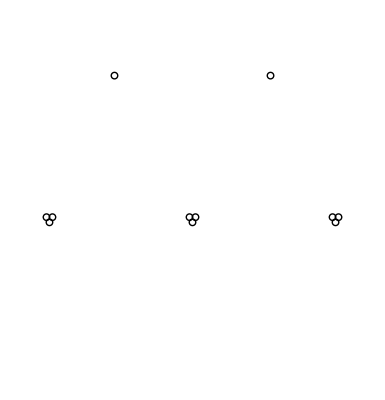

```mathematica
t3=Show[Graphics[mostra3],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
TableForm[Transpose@{Table[i,{i,Length[xc]}],xc,yc}]
```

1 | -11. | 10.736
2 | -10.771 | 11.132
3 | -11.229 | 11.132
4 | 0. | 10.736
5 | 0.229 | 11.132
6 | -0.229 | 11.132
7 | 11. | 10.736
8 | 10.771 | 11.132
9 | 11.229 | 11.132
10 | -6. | 22.
11 | 6. | 22.

### Rail

```mathematica
r0=8.702 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 14.796 10^-3;
ρϕ=29.538 10^-9;  (* [Ω/m] *)
Rdc= ρϕ/(π (r1^2-r0^2));
npr = 2;
nb = 3;
```

```mathematica
{Zf500kVconv,Yf500kVconv}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zf500kVconv 1000]
```

(0.117492+0.704873 ⅈ | 0.0971254+0.37396 ⅈ | 0.0951893+0.323444 ⅈ
0.0971254+0.37396 ⅈ | 0.121027+0.70157 ⅈ | 0.0971254+0.37396 ⅈ
0.0951893+0.323444 ⅈ | 0.0971254+0.37396 ⅈ | 0.117492+0.704873 ⅈ)

```mathematica
Z012500kVConv=Diagonal[ Inverse[A].(Zf500kVconv 1000).A]
```

{0.311631+1.41802 ⅈ,0.0221904+0.34665 ⅈ,0.0221904+0.34665 ⅈ}

```mathematica
MatrixForm[Zf500kVconv 1000]
```

(0.117492+0.704873 ⅈ | 0.0971254+0.37396 ⅈ | 0.0951893+0.323444 ⅈ
0.0971254+0.37396 ⅈ | 0.121027+0.70157 ⅈ | 0.0971254+0.37396 ⅈ
0.0951893+0.323444 ⅈ | 0.0971254+0.37396 ⅈ | 0.117492+0.704873 ⅈ)

```mathematica
Y012500kVConv=I Im@Diagonal[ Inverse[A].(Yf500kVconv 1000).A]
```

{0.+3.56575×10^-6 ⅈ,0.+4.84513×10^-6 ⅈ,0.+4.84513×10^-6 ⅈ}

```mathematica
Zc500kVconv=Sqrt[Z012500kVConv[[2]]/Y012500kVConv[[2]]]
```

267.618-8.55686 ⅈ

```mathematica
Pn500kVconv= 500^2/Re[Zc500kVconv]
```

934.168

```mathematica
500^2/Zc500kVconv
```

933.214+29.8387 ⅈ

```mathematica
ℓ= 120.0;
```

```mathematica
Q500kVconv={{1+Z012500kVConv[[2]]ℓ Y012500kVConv[[2]] ℓ/2, Z012500kVConv[[2]]ℓ}, {Y012500kVConv[[2]] ℓ(1+Z012500kVConv[[2]]ℓ Y012500kVConv[[2]] ℓ/4),1+Z012500kVConv[[2]]ℓ Y012500kVConv[[2]] ℓ/2}};
```

```mathematica
MatrixForm[Q500kVconv]
```

(0.987907+0.000774111 ⅈ | 2.66285+41.598 ⅈ
-2.2504×10^-7+0.0005779 ⅈ | 0.987907+0.000774111 ⅈ)

```mathematica
vr=500. 10^3/Sqrt[3];
```

```mathematica
{vs, is}=Q500kVconv.{500. 10^3/Sqrt[3], 1000 10^3/(Sqrt[3] 500.)}
```

{288259.+48256.8 ⅈ,1140.67+167.719 ⅈ}

```mathematica
Sqrt[3]Abs[vs]/(500 10^3)
```

1.01245

```mathematica
ZL=Z012500kVConv[[2]] ℓ
```

2.66285+41.598 ⅈ

```mathematica
vs
```

288259.+48256.8 ⅈ

```mathematica
iL=(vs-vr)/ZL
```

1154.7+83.9201 ⅈ

```mathematica
perdas= Re[ZL]Abs[iL]^2
```

3.56922×10^6

```mathematica
vsvazio=vs/Q500kVconv[[1,1]]
```

291826.+48618.8 ⅈ

```mathematica
Abs[vsvazio Sqrt[3]]
```

512424.

### usando pu

```mathematica
Sb= 100. 10^6;
Vb= 500. 10^3;
```

```mathematica
Zb= Vb^2/Sb;
Yb= 1/Zb;
```

```mathematica
ib= Sb/(Sqrt[3] Vb)
```

115.47

```mathematica
irpu=(1000 10^3/(Sqrt[3] 500.))/ib
```

10.

```mathematica
Zpu=Z012500kVConv[[2]]ℓ /Zb
```

0.00106514+0.0166392 ⅈ

```mathematica
Ypu= Y012500kVConv[[2]] ℓ/Yb
```

0.+1.45354 ⅈ

```mathematica
QpuConv={{1 +Zpu Ypu/2, Zpu }, {Ypu (1+Zpu Ypu/4),1 +Zpu Ypu/2} };
MatrixForm[QpuConv]
```

(0.987907+0.000774111 ⅈ | 0.00106514+0.0166392 ⅈ
-0.000562601+1.44475 ⅈ | 0.987907+0.000774111 ⅈ)

```mathematica
{vspu, ispu}=QpuConv.{1, irpu}
```

{0.998559+0.167166 ⅈ,9.87851+1.45249 ⅈ}

```mathematica
Abs[vspu]
```

1.01245

```mathematica
Abs[ispu]
```

9.98472

```mathematica
Abs[(vspu -1)/Zpu]^2 Re[Zpu]
```

0.107077

```mathematica
Abs[1/QpuConv[[1,1]]]
```

1.01224

## 500 kV Compacto - Rail

```mathematica
xy4= {{-4.271, 10.771}, {-4.271, 11.229}, {-4.729, 11.229}, {-4.729, 10.771}, {0.229, 15.271},
{0.229, 15.729}, {-0.229, 15.729}, {-0.229, 15.271}, {4.271, 10.771}, {4.271, 11.229},{4.729, 11.229},{4.729, 10.771}, {-3.500, 26.000}, {3.500, 26.000}};
```

```mathematica
mostra4={Circle[#,.25]}&/@xy4;
xc= Table[First[xy4[[i]]], {i,1,Length[xy4]}];
yc =Table[Last[xy4[[i]]], {i,1,Length[xy4]}];
```

```mathematica
yc
```

{10.771,11.229,11.229,10.771,15.271,15.729,15.729,15.271,10.771,11.229,11.229,10.771,26.,26.}

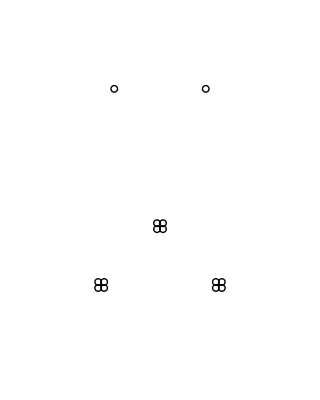

```mathematica
t4=Show[Graphics[mostra4],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},{5,30}},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
nb = 4;
{Z5comp,Y5comp}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Z5comp 1000]
```

(0.111144+0.676122 ⅈ | 0.0974557+0.414473 ⅈ | 0.0945825+0.391039 ⅈ
0.0974557+0.414473 ⅈ | 0.117087+0.67063 ⅈ | 0.0974557+0.414473 ⅈ
0.0945825+0.391039 ⅈ | 0.0974557+0.414473 ⅈ | 0.111144+0.676122 ⅈ)

```mathematica
MatrixForm[Y5comp 1000]
```

(3.×10^-9+5.08966×10^-6 ⅈ | 0.-1.18527×10^-6 ⅈ | 0.-6.26285×10^-7 ⅈ
0.-1.18527×10^-6 ⅈ | 3.×10^-9+5.11653×10^-6 ⅈ | 0.-1.18527×10^-6 ⅈ
0.-6.26285×10^-7 ⅈ | 0.-1.18527×10^-6 ⅈ | 3.×10^-9+5.08966×10^-6 ⅈ)

```mathematica
Z0125comp=Diagonal[ Inverse[A].(Z5comp 1000).A]
```

{0.306121+1.48761 ⅈ,0.0166273+0.267629 ⅈ,0.0166273+0.267629 ⅈ}

```mathematica
Y0125comp=I Im@Diagonal[ Inverse[A].(Y5comp 1000).A]
```

{0.+3.10073×10^-6 ⅈ,0.+6.09755×10^-6 ⅈ,0.+6.09755×10^-6 ⅈ}

```mathematica
Zccomp= Sqrt[Z0125comp[[2]]/Y0125comp[[2]]]
```

209.603-6.50487 ⅈ

```mathematica
Pncomp =500^2/Zccomp
```

1191.58+36.9798 ⅈ

```mathematica
Q5comp={{1+Z0125comp[[2]]ℓ Y0125comp[[2]] ℓ/2, Z0125comp[[2]]ℓ}, {Y0125comp[[2]] ℓ(1+Z0125comp[[2]]ℓ Y0125comp[[2]] ℓ/4),1+Z0125comp[[2]]ℓ Y0125comp[[2]] ℓ/2}};
```

```mathematica
MatrixForm[Q5comp]
```

(0.98825+0.000729979 ⅈ | 1.99528+32.1155 ⅈ
-2.67065×10^-7+0.000727408 ⅈ | 0.98825+0.000729979 ⅈ)

```mathematica
{vsc, isc}=Q5comp.{500. 10^3/Sqrt[3], 1000 10^3/(Sqrt[3] 500.)}
```

{287587.+37294.5 ⅈ,1141.06+210.827 ⅈ}

```mathematica
Sqrt[3]Abs[vsc]/(500 10^3)
```

1.00457

```mathematica
ZLc=Z0125comp[[2]] ℓ
```

1.99528+32.1155 ⅈ

```mathematica
iLc=(vsc-vr)/ZLc
```

1154.7+105.613 ⅈ

```mathematica
perdas= Re[ZLc]Abs[iLc]^2
```

2.68263×10^6

```mathematica
vsvazio=vsc/Q5comp[[1,1]]
```

291034.+37522.9 ⅈ

```mathematica
Abs[vsvazio Sqrt[3]]
```

508258.

## Circuito Duplo 500 kV - Rail

```mathematica
db=.475;
xc=Flatten@Outer[Plus,{6,11,6+9},db Cos[π/4 +#1 π/2]&@Range[0,3]];
xc=Flatten[Join[xc,-xc]];
yc=Flatten@Outer[Plus,{27.7-4.5,27.7+10-4.5, 27.7-4.5},db Sin[π/4 +#1 π/2]&@Range[0,3]];
yc=Flatten[Join[yc,yc]];
xc=Flatten[Join[xc,{8.8,-8.8}]];
yc=Flatten[Join[yc,{27.7+10+5,27.7+10+5}]];
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.09]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,
BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotRange->{Automatic,{10,Max[yc]+5 }},FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

```mathematica
TableForm[Transpose@{Table[i,{i,Length[xc]}],xc,yc}]
```

1 | 6.33588 | 23.5359
2 | 5.66412 | 23.5359
3 | 5.66412 | 22.8641
4 | 6.33588 | 22.8641
5 | 11.3359 | 33.5359
6 | 10.6641 | 33.5359
7 | 10.6641 | 32.8641
8 | 11.3359 | 32.8641
9 | 15.3359 | 23.5359
10 | 14.6641 | 23.5359
11 | 14.6641 | 22.8641
12 | 15.3359 | 22.8641
13 | -6.33588 | 23.5359
14 | -5.66412 | 23.5359
15 | -5.66412 | 22.8641
16 | -6.33588 | 22.8641
17 | -11.3359 | 33.5359
18 | -10.6641 | 33.5359
19 | -10.6641 | 32.8641
20 | -11.3359 | 32.8641
21 | -15.3359 | 23.5359
22 | -14.6641 | 23.5359
23 | -14.6641 | 22.8641
24 | -15.3359 | 22.8641
25 | 8.8 | 42.7
26 | -8.8 | 42.7

```mathematica
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.10668+0.659443 ⅈ | 0.0931211+0.376972 ⅈ | 0.0891524+0.396939 ⅈ | 0.0900953+0.374309 ⅈ | 0.0929291+0.334321 ⅈ | 0.0890368+0.333217 ⅈ
0.0931211+0.376972 ⅈ | 0.11311+0.653831 ⅈ | 0.092099+0.38076 ⅈ | 0.0929291+0.334321 ⅈ | 0.0958972+0.323343 ⅈ | 0.091734+0.309408 ⅈ
0.0891524+0.396939 ⅈ | 0.092099+0.38076 ⅈ | 0.104752+0.66131 ⅈ | 0.0890368+0.333217 ⅈ | 0.091734+0.309408 ⅈ | 0.0880088+0.307321 ⅈ
0.0900953+0.374309 ⅈ | 0.0929291+0.334321 ⅈ | 0.0890368+0.333217 ⅈ | 0.10668+0.659443 ⅈ | 0.0931211+0.376972 ⅈ | 0.0891524+0.396939 ⅈ
0.0929291+0.334321 ⅈ | 0.0958972+0.323343 ⅈ | 0.091734+0.309408 ⅈ | 0.0931211+0.376972 ⅈ | 0.11311+0.653831 ⅈ | 0.092099+0.38076 ⅈ
0.0890368+0.333217 ⅈ | 0.091734+0.309408 ⅈ | 0.0880088+0.307321 ⅈ | 0.0891524+0.396939 ⅈ | 0.092099+0.38076 ⅈ | 0.104752+0.66131 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+5.12268×10^-6 ⅈ | 0.-8.3778×10^-7 ⅈ | 0.-1.1262×10^-6 ⅈ | 0.-7.88134×10^-7 ⅈ | 0.-3.03062×10^-7 ⅈ | 0.-2.16443×10^-7 ⅈ
0.-8.3778×10^-7 ⅈ | 3.×10^-9+4.84752×10^-6 ⅈ | 0.-9.90703×10^-7 ⅈ | 0.-3.03062×10^-7 ⅈ | 0.-3.44091×10^-7 ⅈ | 0.-1.28253×10^-7 ⅈ
0.-1.1262×10^-6 ⅈ | 0.-9.90703×10^-7 ⅈ | 3.×10^-9+4.9221×10^-6 ⅈ | 0.-2.16443×10^-7 ⅈ | 0.-1.28253×10^-7 ⅈ | 0.-7.97511×10^-8 ⅈ
0.-7.88134×10^-7 ⅈ | 0.-3.03062×10^-7 ⅈ | 0.-2.16443×10^-7 ⅈ | 3.×10^-9+5.12268×10^-6 ⅈ | 0.-8.3778×10^-7 ⅈ | 0.-1.1262×10^-6 ⅈ
0.-3.03062×10^-7 ⅈ | 0.-3.44091×10^-7 ⅈ | 0.-1.28253×10^-7 ⅈ | 0.-8.3778×10^-7 ⅈ | 3.×10^-9+4.84752×10^-6 ⅈ | 0.-9.90703×10^-7 ⅈ
0.-2.16443×10^-7 ⅈ | 0.-1.28253×10^-7 ⅈ | 0.-7.97511×10^-8 ⅈ | 0.-1.1262×10^-6 ⅈ | 0.-9.90703×10^-7 ⅈ | 3.×10^-9+4.9221×10^-6 ⅈ)

```mathematica
Aplus=ArrayFlatten[{{A,0},{0, A}}];
```

```mathematica
MatrixForm[Abs[Inverse[Aplus].(Zabc 1000) . Aplus]]
```

(1.45734 | 0.00903586 | 0.00927231 | 1.02359 | 0.0247163 | 0.0317171
0.00927231 | 0.273816 | 0.00994519 | 0.0317171 | 0.00934285 | 0.00514328
0.00903586 | 0.0100643 | 0.273816 | 0.0247163 | 0.00536225 | 0.00934285
1.02359 | 0.0247163 | 0.0317171 | 1.45734 | 0.00903586 | 0.00927231
0.0317171 | 0.00934285 | 0.00514328 | 0.00927231 | 0.273816 | 0.00994519
0.0247163 | 0.00536225 | 0.00934285 | 0.00903586 | 0.0100643 | 0.273816)

```mathematica
Zsq2=Diagonal[ Inverse[Aplus].(Zabc 1000) . Aplus]
```

{0.291096+1.42797 ⅈ,0.0167231+0.273305 ⅈ,0.0167231+0.273305 ⅈ,0.291096+1.42797 ⅈ,0.0167231+0.273305 ⅈ,0.0167231+0.273305 ⅈ}

```mathematica
Ysq2=Diagonal[ Inverse[Aplus].(Yabc 1000) . Aplus]
```

{3.×10^-9+2.99431×10^-6 ⅈ,3.×10^-9+5.94899×10^-6 ⅈ,3.×10^-9+5.94899×10^-6 ⅈ,3.×10^-9+2.99431×10^-6 ⅈ,3.×10^-9+5.94899×10^-6 ⅈ,3.×10^-9+5.94899×10^-6 ⅈ}

```mathematica
Zc2c=Sqrt[Zsq2/Ysq2]
```

{694.153-69.6809 ⅈ,214.441-6.50043 ⅈ,214.441-6.50043 ⅈ,694.153-69.6809 ⅈ,214.441-6.50043 ⅈ,214.441-6.50043 ⅈ}

```mathematica
Pn=(500. )^2/Re[Zc2c[[2]]]
```

1165.82

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu
Investigar o comportamento das matrizes de impedância e admitância de sequências, supondo o circuito transposto

## 500 kV Recapacitado - Rail

```mathematica
xy2={{-7.229, 8.639}, {-7.229, 10.500}, {-6.771, 10.500}, {-6.771, 8.639}, {-0.229, 10.500},
{-0.229, 9.876}, {0.229, 9.876}, {0.229, 10.500}, {7.229, 8.639}, {7.229, 10.500}, {6.771, 10.500},
{6.771, 8.639}, {-5.000, 20.500}, {5.000, 20.500}};
```

```mathematica
mostra2={Circle[#,.25]}&/@xy2;
xc= Table[First[xy2[[i]]], {i,1,Length[xy2]}];
yc =Table[Last[xy2[[i]]], {i,1,Length[xy2]}];
```

```mathematica
TableForm[Transpose@{Table[i,{i,Length[xc]}],xc,yc}]
```

1 | -7.229 | 8.639
2 | -7.229 | 10.5
3 | -6.771 | 10.5
4 | -6.771 | 8.639
5 | -0.229 | 10.5
6 | -0.229 | 9.876
7 | 0.229 | 9.876
8 | 0.229 | 10.5
9 | 7.229 | 8.639
10 | 7.229 | 10.5
11 | 6.771 | 10.5
12 | 6.771 | 8.639
13 | -5. | 20.5
14 | 5. | 20.5

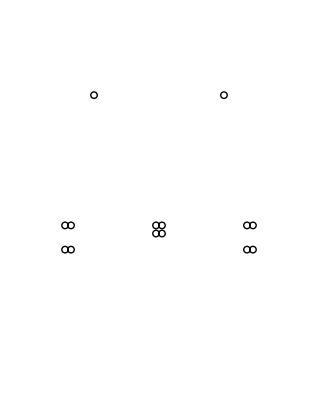

```mathematica
t2=Show[Graphics[mostra2],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},{-.10,25}},FrameLabel->{"x (m)","y (m)"}]
```

```mathematica
{Z5r,Y5r}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Z5r 1000]
```

(0.114357+0.626587 ⅈ | 0.0990428+0.40516 ⅈ | 0.0976523+0.354856 ⅈ
0.0990428+0.40516 ⅈ | 0.116917+0.661847 ⅈ | 0.0990428+0.40516 ⅈ
0.0976523+0.354856 ⅈ | 0.0990428+0.40516 ⅈ | 0.114357+0.626587 ⅈ)

```mathematica
MatrixForm[Y5r 1000]
```

(3.×10^-9+5.94805×10^-6 ⅈ | 0.-1.21925×10^-6 ⅈ | 0.-3.25131×10^-7 ⅈ
0.-1.21925×10^-6 ⅈ | 3.×10^-9+5.46085×10^-6 ⅈ | 0.-1.21925×10^-6 ⅈ
0.-3.25131×10^-7 ⅈ | 0.-1.21925×10^-6 ⅈ | 3.×10^-9+5.94805×10^-6 ⅈ)

```mathematica
Z0125r=Diagonal[ Inverse[A].(Z5r 1000).A]
```

{0.312369+1.41512 ⅈ,0.0166312+0.249949 ⅈ,0.0166312+0.249949 ⅈ}

```mathematica
Y0125r=I Im@Diagonal[ Inverse[A].(Y5r 1000).A]
```

{0.+3.94323×10^-6 ⅈ,0.+6.70686×10^-6 ⅈ,0.+6.70686×10^-6 ⅈ}

```mathematica
Zcr= Sqrt[Z0125r[[2]]/Y0125r[[2]]]
```

193.155-6.41902 ⅈ

```mathematica
Pnr =500^2/Zcr
```

1292.87+42.9653 ⅈ

```mathematica
Q5r={{1+Z0125r[[2]]ℓ Y0125r[[2]] ℓ/2, Z0125r[[2]]ℓ}, {Y0125r[[2]] ℓ(1+Z0125r[[2]]ℓ Y0125r[[2]] ℓ/4),1+Z0125r[[2]]ℓ Y0125r[[2]] ℓ/2}};
```

```mathematica
MatrixForm[Q5r]
```

(0.98793+0.000803111 ⅈ | 1.99575+29.9939 ⅈ
-3.23181×10^-7+0.000799966 ⅈ | 0.98793+0.000803111 ⅈ)

```mathematica
{vsr, isr}=Q5r.{500. 10^3/Sqrt[3], 1000 10^3/(Sqrt[3] 500.)}
```

{287495.+34865.8 ⅈ,1140.67+231.858 ⅈ}

```mathematica
Sqrt[3]Abs[vsr]/(500 10^3)
```

1.00321

```mathematica
ZLr=Z0125r[[2]] ℓ
```

1.99575+29.9939 ⅈ

```mathematica
iLr=(vsr-vr)/ZLr
```

1154.7+116.166 ⅈ

```mathematica
perdas= Re[ZLr]Abs[iLr]^2
```

2.68793×10^6

```mathematica
vsvazio=vsr/Q5r[[1,1]]
```

291036.+35055.1 ⅈ

```mathematica
Abs[vsvazio Sqrt[3]]
```

507733.

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu

## 500 kV expandido 1

condutor de fase bittern, cabo pararraios 3/8 EHS

```mathematica
xy5={{-5.754,9.543},{-4.496,10.314},{-4.977,11.562},{-6.529,11.562},{-7.009,10.314},{0.000,13.845},{0.866,14.409},{0.535,15.317},{-0.535,15.317},{-0.866,14.409},{5.754,9.543},{4.496,10.314},{4.977,11.562},{6.529,11.562},{7.009,10.314},{-4.000,23.961},{4.000,23.961}};
```

```mathematica
xc= xy5[[1;;,1]];
```

```mathematica
yc= xy5[[1;;,2]];
```

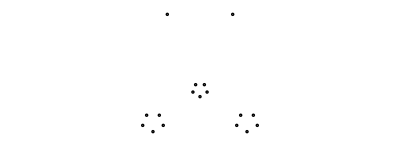

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-20,20},All},FrameTicks->{{-10,0,10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
nb = 5;
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.109258+0.583972 ⅈ | 0.0989162+0.405596 ⅈ | 0.095798+0.371846 ⅈ
0.0989162+0.405596 ⅈ | 0.115586+0.598055 ⅈ | 0.0989162+0.405596 ⅈ
0.095798+0.371846 ⅈ | 0.0989162+0.405596 ⅈ | 0.109258+0.583972 ⅈ)

```mathematica
Zseqe=Diagonal[Inverse[A]. (Zabc 1000). A]
```

{0.307121+1.37736 ⅈ,0.0134907+0.19432 ⅈ,0.0134907+0.19432 ⅈ}

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+7.18102×10^-6 ⅈ | 0.-1.93222×10^-6 ⅈ | 0.-7.06818×10^-7 ⅈ
0.-1.93222×10^-6 ⅈ | 3.×10^-9+6.87933×10^-6 ⅈ | 0.-1.93222×10^-6 ⅈ
0.-7.06818×10^-7 ⅈ | 0.-1.93222×10^-6 ⅈ | 3.×10^-9+7.18102×10^-6 ⅈ)

```mathematica
Yseqe= Diagonal[Inverse[A].(Yabc 1000).A]
```

{3.×10^-9+4.03296×10^-6 ⅈ,3.×10^-9+8.60421×10^-6 ⅈ,3.×10^-9+8.60421×10^-6 ⅈ}

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu

## 500 kV expandido 2

condutor de fase grackle, cabo pararraios 3/8 EHS

```mathematica
xc={-5.975,-5.6499999999999995,-5.975,-6.625,-6.95,-6.625,0.32499999999999996,0.65,0.32500000000000023,-0.32499999999999984,-0.65,-0.3250000000000003,6.625,6.95,6.625,5.975,5.6499999999999995,5.975,-8.5,8.5};
```

```mathematica
yc={33.59045641596338,34.62968690050471,35.668917385046036,35.668917385046036,34.62968690050471,33.59045641596338,34.09045641596338,35.12968690050471,36.168917385046036,36.168917385046036,35.12968690050471,34.09045641596338,33.59045641596338,34.62968690050471,35.668917385046036,35.668917385046036,34.62968690050471,33.59045641596338,42.32968690050471,42.32968690050471};
```

```mathematica
TableForm[Transpose@{Table[i,{i,Length[xc]}],xc,yc}]
```

1 | -5.975 | 33.5905
2 | -5.65 | 34.6297
3 | -5.975 | 35.6689
4 | -6.625 | 35.6689
5 | -6.95 | 34.6297
6 | -6.625 | 33.5905
7 | 0.325 | 34.0905
8 | 0.65 | 35.1297
9 | 0.325 | 36.1689
10 | -0.325 | 36.1689
11 | -0.65 | 35.1297
12 | -0.325 | 34.0905
13 | 6.625 | 33.5905
14 | 6.95 | 34.6297
15 | 6.625 | 35.6689
16 | 5.975 | 35.6689
17 | 5.65 | 34.6297
18 | 5.975 | 33.5905
19 | -8.5 | 42.3297
20 | 8.5 | 42.3297

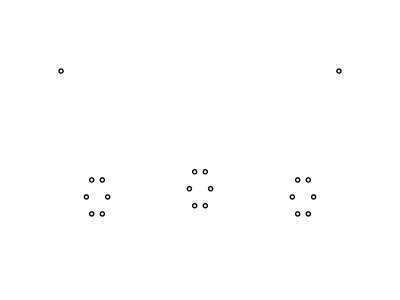

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},{30, 45}},FrameTicks->{{-10,0,10},{30,35,40,45},False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
nb = 6;
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.111632+0.588971 ⅈ | 0.100553+0.412206 ⅈ | 0.0998673+0.361985 ⅈ
0.100553+0.412206 ⅈ | 0.111981+0.588256 ⅈ | 0.100553+0.412206 ⅈ
0.0998673+0.361985 ⅈ | 0.100553+0.412206 ⅈ | 0.111632+0.588971 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+6.47095×10^-6 ⅈ | 0.-2.47082×10^-6 ⅈ | 0.-7.28741×10^-7 ⅈ
0.-2.47082×10^-6 ⅈ | 3.×10^-9+7.30771×10^-6 ⅈ | 0.-2.47082×10^-6 ⅈ
0.-7.28741×10^-7 ⅈ | 0.-2.47082×10^-6 ⅈ | 3.×10^-9+6.47095×10^-6 ⅈ)

```mathematica
Z012c6=Diagonal[ Inverse[A].(Zabc 1000).A]
```

{0.312397+1.37966 ⅈ,0.0114244+0.193267 ⅈ,0.0114244+0.193267 ⅈ}

```mathematica
Y012c6=I Im@Diagonal[ Inverse[A].(Yabc 1000).A]
```

{0.+2.96962×10^-6 ⅈ,0.+8.63999×10^-6 ⅈ,0.+8.63999×10^-6 ⅈ}

```mathematica
Zcr= Sqrt[Z012c6[[2]]/Y012c6[[2]]]
```

149.627-4.41855 ⅈ

```mathematica
Pnr =500^2/Zcr
```

1669.36+49.2968 ⅈ

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu

## LT 500 kV expandido 3

```mathematica
nfase=3;
nb=5;
npr=2;
ncond=nfase*nb+npr;
```

dados dos condutores obtidos a partir do arquivo LT500kV baseado na torre de 400kV Portela para a Africa

```mathematica
xy6={{-6.722,9.543},{-5.739,10.918},{-6.115,13.139},{-7.330,13.139},{-7.706,10.918},{0.000,10.622},{0.750,11.250},{0.465,12.267},{-0.465,12.267},{-0.750,11.250},{6.722,9.543},{5.739,10.918},{6.115,13.139},{7.330,13.139},{7.706,10.918},{5.000,23.941},{-5.000,23.941}};
```

```mathematica
xc= xy6[[1;;,1]];
yc= xy6[[1;;,2]];
```

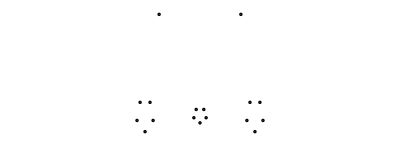

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-20,20},All},FrameTicks->{{-10,0,10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.109718+0.570959 ⅈ | 0.0970808+0.409354 ⅈ | 0.0961778+0.359353 ⅈ
0.0970808+0.409354 ⅈ | 0.111204+0.603535 ⅈ | 0.0970808+0.409354 ⅈ
0.0961778+0.359353 ⅈ | 0.0970808+0.409354 ⅈ | 0.109718+0.570959 ⅈ)

```mathematica
Zseqe=Diagonal[Inverse[A]. (Zabc 1000). A]
```

{0.303773+1.36719 ⅈ,0.0134335+0.189131 ⅈ,0.0134335+0.189131 ⅈ}

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+7.4518×10^-6 ⅈ | 0.-2.08649×10^-6 ⅈ | 0.-5.36242×10^-7 ⅈ
0.-2.08649×10^-6 ⅈ | 3.×10^-9+7.10292×10^-6 ⅈ | 0.-2.08649×10^-6 ⅈ
0.-5.36242×10^-7 ⅈ | 0.-2.08649×10^-6 ⅈ | 3.×10^-9+7.4518×10^-6 ⅈ)

```mathematica
Yseqe=Diagonal[Inverse[A]. (Yabc 1000). A]
```

{3.×10^-9+4.19603×10^-6 ⅈ,3.×10^-9+8.90525×10^-6 ⅈ,3.×10^-9+8.90525×10^-6 ⅈ}

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu

## 345kV - Ruddy

### Ruddy

```mathematica
r0=7.821 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 14.364 10^-3;
ρϕ=29.559 10^-9;  (* [Ω/m] *)
Rdc= ρϕ/(π (r1^2-r0^2));
npr = 2;
nb = 2;
```

```mathematica
xy1={{-7.229,10.5}, {-6.771, 10.500}, {-0.229, 10.500}, {0.229, 10.500}, {7.229, 10.500},
{6.771, 10.500}, {-5.000, 20.500}, {5.000, 20.500}};
```

```mathematica
mostra1={Circle[#,.25]}&/@xy1;
```

```mathematica
t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10.1,10.1},{0,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

-Graphics-

```mathematica
xc= xy1[[1;;,1]];
yc= xy1[[1;;,2]];
```

```mathematica
TableForm[Transpose@{Table[i,{i,Length[xc]}],xc,yc}]
```

1 | -7.229 | 10.5
2 | -6.771 | 10.5
3 | -0.229 | 10.5
4 | 0.229 | 10.5
5 | 7.229 | 10.5
6 | 6.771 | 10.5
7 | -5. | 20.5
8 | 5. | 20.5

```mathematica
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.131486+0.74797 ⅈ | 0.0997481+0.405547 ⅈ | 0.0986202+0.354267 ⅈ
0.0997481+0.405547 ⅈ | 0.133464+0.746103 ⅈ | 0.0997481+0.405547 ⅈ
0.0986202+0.354267 ⅈ | 0.0997481+0.405547 ⅈ | 0.131486+0.74797 ⅈ)

```mathematica
Z012=Diagonal[Inverse[A]. (Zabc 1000). A]
```

{0.33089+1.52425 ⅈ,0.0327733+0.358894 ⅈ,0.0327733+0.358894 ⅈ}

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+4.03799×10^-6 ⅈ | 0.-6.94947×10^-7 ⅈ | 0.-1.996×10^-7 ⅈ
0.-6.94947×10^-7 ⅈ | 3.×10^-9+4.16925×10^-6 ⅈ | 0.-6.94947×10^-7 ⅈ
0.-1.996×10^-7 ⅈ | 0.-6.94947×10^-7 ⅈ | 3.×10^-9+4.03799×10^-6 ⅈ)

```mathematica
Y012= Diagonal[Inverse[A]. (Yabc 1000). A]
```

{3.×10^-9+3.02208×10^-6 ⅈ,3.×10^-9+4.61158×10^-6 ⅈ,3.×10^-9+4.61158×10^-6 ⅈ}

```mathematica
Zc=Sqrt[Z012[[2]]/Y012[[2]]]
```

279.265-12.6334 ⅈ

```mathematica
Pn= 345^2/Zc
```

425.338+19.2415 ⅈ

```mathematica
10^5 Z012[[2]]100/(345^2)
```

2.75348+30.1528 ⅈ

```mathematica
Y012[[2]](345^2)/100
```

3.57075×10^-6+0.00548893 ⅈ

## LT 230 kV circuito 1

condutor de fase Grossbeak, pararraios 3/8” EHS

```mathematica
xc={-7.5, 0, 7.5, -4.7, 4.7};
yc= {21,21,21,25, 25}-2/3 {12.8, 12.8, 12.8, 8.85, 8.85};
```

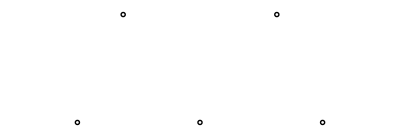

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},All},FrameTicks->{{-10,-5, 0,5, 10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

## LT 230 kV circuito 2

condutor de fase Grossbeak, pararraios 3/8” EHS

```mathematica
xc={-3.8, 3.8, -3.8, -2.4, 2.4};
yc= {28.1,31.1,28.1+5.9,28.1+5.9+7.8,28.1+5.9+7.8}-2/3 {14.6, 14.6, 14.6, 8.7, 8.7};
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},All},FrameTicks->{{-10,-5, 0,5, 10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

-Graphics-

## LT 230 kV Circuito Duplo

condutor de fase Grossbeak, pararraios 3/8” EHS

```mathematica
yc={22.15185227641591,28.15185227641591,34.15185227641591,22.15185227641591,28.15185227641591,34.15185227641591,39.15185227641591,39.15185227641591};
```

```mathematica
xc={-4.3,-4.3,-4.3,4.3,4.3,4.3,-3.8,3.8};
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},All},FrameTicks->{{-10,-5, 0,5, 10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

-Graphics-